```mathematica
(*Power[z , 4]*)
```

```mathematica
(*z (CTRL + 6) 2*)
```

```mathematica
solution = Solve[z^4==1 , z];
```

```mathematica
(*f[x] == x//f*)
```

```mathematica
solution//Length
```

4

```mathematica
z/.solution[[1]]
```

-1

```mathematica
z/.solution[[2]]
```

-ⅈ

```mathematica
-1
```

```mathematica
z/.solution[[3]]
```

ⅈ

```mathematica
z/.solution[[4]]
```

1

```mathematica
solution
```

{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1}}

```mathematica
z/.solution
```

{-1,-ⅈ,ⅈ,1}

```mathematica
z^4==1/.solution[[2]]
```

True

```mathematica
z^4==1/.solution
```

{True,True,True,True}

```mathematica
Solve[z^4==1 , z , Reals]
```

{{z→-1},{z→1}}

```mathematica
ala/.ala->kota
```

kota

```mathematica
Hold[FullForm[ala/.ala->kota]]
```

Hold[ReplaceAll[ala,Rule[ala,kota]]]

```mathematica
(*->*)
```

```mathematica
f[g[h[x] , y]]/.{x->1 , y->2}
```

f[g[h[1],2]]

```mathematica
FullForm[x->1]
```

Rule[x,1]

```mathematica
mySolution = {{3 , 4 , 5} , {5 , 12 , 13} , {8 , 15 , 17}};
```

```mathematica
mySolution[[;;,1;;2]]
```

{{3,4},{5,12},{8,15}}

```mathematica
Flatten[mySolution[[;;,1;;2]]]
```

{3,4,5,12,8,15}

```mathematica
NSolve[z^4==1 , z]
```

{{z→-1.},{z→0.-1. ⅈ},{z→0.+1. ⅈ},{z→1.}}

```mathematica
myRealSolution = Solve[z^4==1 , z , Reals]
```

{{z→-1},{z→1}}

```mathematica
myRealSolutionValue = z/.myRealSolution
```

{-1,1}

```mathematica
(*1 (CTRL + /) 2*)
```

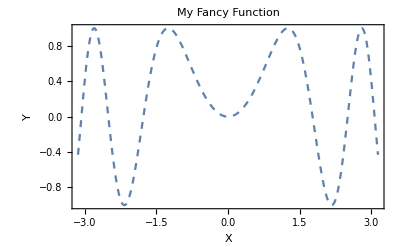

```mathematica
Plot[Sin[x^2] , {x , -π , π} , PlotStyle-> Dashed , Axes->False , Frame->True , FrameLabel->{"X" , "Y"} , PlotLabel->"My Fancy Function" , GridLines->{{0 , π , -π , π/2 , -π/2} , None}]
```

```mathematica
N[π (1/2)^2]
```

0.785398

```mathematica
f[x_ , y_]:=If[x^2 + y^2<0.5^2 , 1.0 , 0.0];
```

```mathematica
NIntegrate[f[x , y] , {x , -1 , 1},{y , -1 , 1}]
```

0.785398

```mathematica
π (1/2)^2
```

π/4

```mathematica
(*Integrate*)
```